# The Twitter Service Object

The Twitter ServiceObject is one of the external $Services ‘curated’ by Wolfram Research.

```mathematica
twitter = ServiceConnect["Twitter"]
```

ServiceObject[…]

Every ServiceObject has “standard properties” supported by all services such as Information and Requests (list of parameters):

```mathematica
twitter["Information"]
```

A service for sending and receiving tweets from a Twitter account

```mathematica
twitter["Requests"]
```

{Authentication,FollowerIDs,FollowerMentionNetwork,FollowerNetwork,FollowerReplyToNetwork,Followers,FriendIDs,FriendMentionNetwork,FriendNetwork,FriendReplyToNetwork,Friends,GetTweet,ID,ImageTweet,Information,LastTweet,Name,RateLimit,RawRequests,Retweet,SearchMentionNetwork,SearchNetwork,SearchReplyToNetwork,Tweet,TweetEventSeries,TweetList,TweetSearch,TweetTimeline,UserData,UserHashtags,UserIDSearch,UserMentions,UserReplies}

```mathematica
twitter["RateLimit"]
```

Dataset[<>]

```mathematica
twitter["UserData"]
```

{<|ID→67803525,Name→Bryan D. Wilhite,ScreenName→BryanWilhite,Location→California,FollowersCount→366,FriendsCount→637,FavouritesCount→24|>}

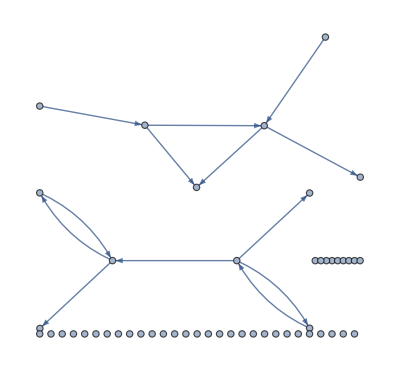

```mathematica
twitter["FriendMentionNetwork"]
```